```mathematica
valLstLst=readJuliaVarSqDim["GOE_RSym_Lst.jld2","valLstLst"];
```

```mathematica
valLstLst//Dimensions
```

{6,6,6,100,100}

```mathematica
valLstLst⟦1,1,1⟧//Dimensions
```

{100,100}

```mathematica
valDiffLst
```

```mathematica
valAllLst=Table[Flatten[valLstLst⟦ii,jj,kk⟧],{ii,1,6},{jj,1,6},{kk,1,6}];
valDiffLst=Table[Flatten[(RotateLeft[valLstLst⟦ii,jj,kk⟧,{0,1}]-valLstLst⟦ii,jj,kk⟧)⟦All,1;;-2⟧],{ii,1,6},{jj,1,6},{kk,1,6}];
```

```mathematica
spectDatLst=Table[histLstToDat[HistogramList[valAllLst⟦ii,jj,kk⟧]],{ii,1,6},{jj,1,6},{kk,1,6}];
```

```mathematica
diffDatLst=Table[histLstToDat[HistogramList[valDiffLst⟦ii,jj,kk⟧]],{ii,1,6},{jj,1,6},{kk,1,6}];
```

```mathematica
diffDatLst=Table[]
```

```mathematica
Flatten[spectDatLst,2]//Dimensions
```

{216}

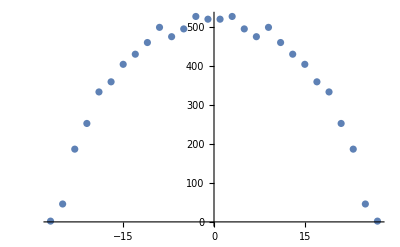

```mathematica
ListPlot[spectDatLst⟦1,1,1⟧]
```

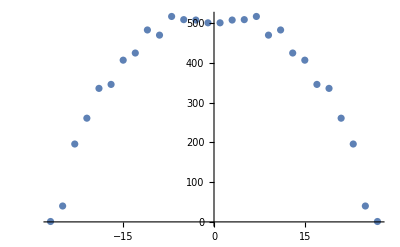

```mathematica
ListPlot[spectDatLst⟦2,1,1⟧]
```

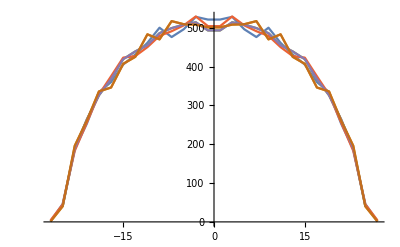

```mathematica
ListLinePlot[spectDatLst⟦All,1,1⟧]
```

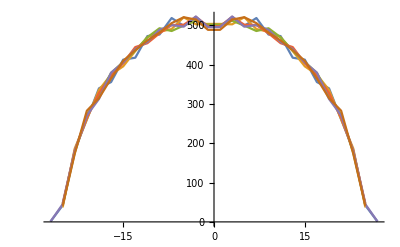

```mathematica
ListLinePlot[spectDatLst⟦All,2,1⟧]
```

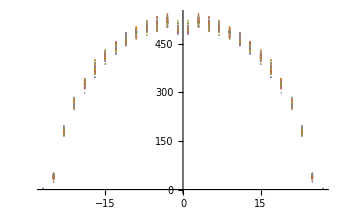

```mathematica
ListPlot[Flatten[spectDatLst,2]]
```

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"\\Delta E", "\\mathrm{occurences}"};
```

```mathematica
legX3Lst=MaTeX[#,Magnification->labMag]&/@{"0","\\pi/3","2\\pi / 3", "\\pi", "4\\pi/3","5\\pi/3"};
```

```mathematica
legX3Lab=MaTeX["\\theta_3 = \\qquad",Magnification->labMag];
```

```mathematica
titleX3=MaTeX["\\theta_1 = \\theta_2 = 0", Magnification->labMag];
```

```mathematica
legX3Lst
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

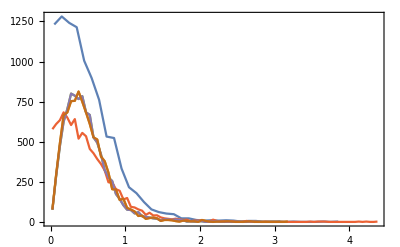

```mathematica
ListLinePlot[diffDatLst⟦All,1,1⟧,ImageSize->{Automatic,6cm},PlotLabel->titleX3,Frame->True,FrameLabel->xyLabs,PlotRangePadding->None,PlotLegends->LineLegend[legX3Lst,LegendLabel->legX3Lab,Spacings->Small]]
```

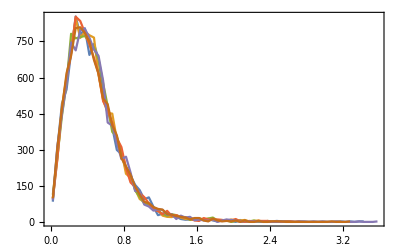

```mathematica
ListLinePlot[diffDatLst⟦All,2,1⟧,ImageSize->{Automatic,6cm},Frame->True,FrameLabel->xyLabs,PlotRangePadding->None,PlotLegends->LineLegend[legX3Lst,LegendLabel->legX3Lab,Spacings->Small]]
```

```mathematica
valLstDiff=(RotateLeft[valLstLst,{0,1}]-valLstLst)⟦All,1;;-2⟧;
```

```mathematica
valLstAll=Flatten[valLstLst];
```

```mathematica
valLstDiffAll=Flatten[valLstDiff];
```

```mathematica
diffDat=histLstToDat[HistogramList[valLstDiffAll]];
```

```mathematica
spectDat=histLstToDat[HistogramList[valLstAll]];
```

```mathematica
{binWalls,binVals}=HistogramList[valLstAll];
```

```mathematica
binMids=((binWalls+RotateLeft[binWalls,1])/2)⟦1;;-2⟧;
```

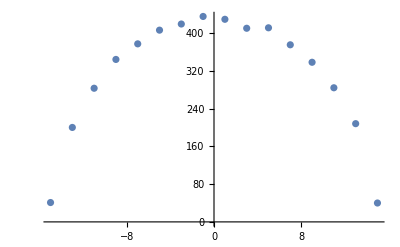

```mathematica
ListPlot[{binMids,binVals}ᵀ]
```

```mathematica
mat1={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
RotateLeft[mat1,{0,1}]
```

{{2,3,1},{5,6,4}}

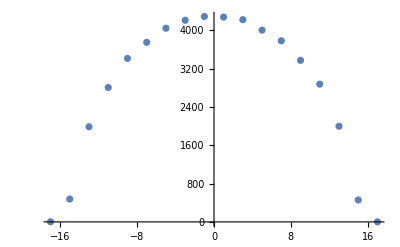

```mathematica
ListPlot[spectDat]
```

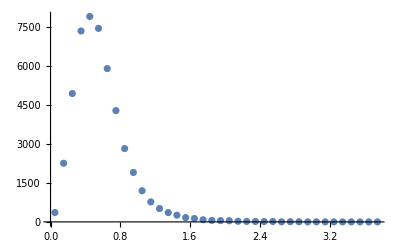

```mathematica
ListPlot[diffDat]
```

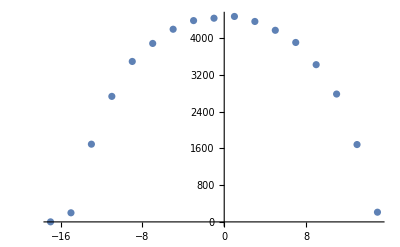

```mathematica
ListPlot[spectDat]
```

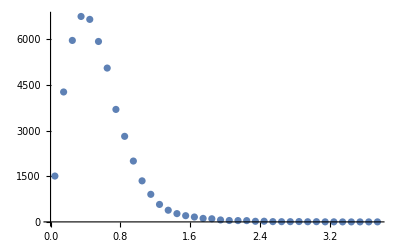

```mathematica
ListPlot[diffDat]
```